```mathematica
<<Braindrop`
```

### DAC Mismatch

Let the transistor threshold difference, normalized by U_T, be \[Distributed] Normal[0, σ].  
Let the current through branch B_i be I_i. The termination branch has current I_T
Let I_0 be our reference LSB current through branch B_0. Since we are dealing with ratios of currents with respect to I_0, we don’t need to include a mismatch term for I_0. That is, we always consider the LSB bit 0’s current, I_0, to be correct.

Between the bit 0 and tail, we have the current through both as

I_(0:T)= I_0(1+α_T)

The current for bit 1 is then

I_1= α_1 I_(0:T)= α_1(1+α_T) I_0

and the total current through bits 1 and 0 is

I_(1:0) = I_1 + I_0 = α_1(1+α_T) I_0+I_0=α_1(1+α_T) I_0+I_0(1+α_T)-α_T I_0=(1+α_1)(1+α_T)I_0-α_T I_0

Extending this, for any bit i≥1, we have

```mathematica
R2R`branchCurrent[i_]:= Subscript[I, 0] Subscript[α, i]∏_(j=0)^(i-1) (1+Subscript[α, j])/;i>0||¬NumberQ[i];
R2R`branchCurrent[0]:= Subscript[I, 0];
R2R`totalCurrent[i_]:=Subscript[I, 0]∏_(j=0)^i (1+Subscript[α, j]);
R2R`totalBitCurrent[i_]:=R2R`totalCurrent[i]-Subscript[α, 0] Subscript[I, 0];
TableForm[Style[#,"Output"]&/@#&/@{{Subscript[I, i], R2R`branchCurrent[i], Subscript[α, 0]⧦Subscript[α, T]},
{Subscript[I, i:T], R2R`totalCurrent[i], ""},
{Subscript[I, i:0], R2R`totalBitCurrent[i], ""}}]
```

I_i | I_0 (∏_(j=0)^(-1+i) (1+α_j)) α_i | α_0⧦α_T
I_(i:T) | I_0 ∏_(j=0)^i (1+α_j) | 
I_(i:0) | I_0 ∏_(j=0)^i (1+α_j)-I_0 α_0 |

The % difference (in terms of I_0) between any MSB i and all its LSBs (i.e., DNL) is then

Δ_i=(I_i-I_(i-1:0))/I_0-1
This is given by

```mathematica
R2R`DNL[i_]:=Simplify[(R2R`branchCurrent[i]-R2R`totalBitCurrent[i-1])/Subscript[I, 0]-1]/;i>0||¬NumberQ[i];
R2R`DNL[0]=0;
FullSimplify[R2R`DNL[i]]
```

-1+α_0+(∏_(j=0)^(-1+i) (1+α_j)) (-1+α_i)

Give below are I_i, I_(i:0), I_(i;T) and Δ_i when there is no mismatch.

```mathematica
Grid[Transpose[Flatten[Append[{{{B,Subscript[I, i], Subscript[I, i:0], Subscript[I, i:T], Subscript[Δ, i]}}},{#+1,R2R`branchCurrent[#],R2R`totalBitCurrent[#],R2R`totalCurrent[#],R2R`DNL[#]}/.Subscript[α, _]-> 1&/@Range[0, 9]],1]], Dividers-> {2-> True,None}]
```

B | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
I_i | I_0 | 2 I_0 | 4 I_0 | 8 I_0 | 16 I_0 | 32 I_0 | 64 I_0 | 128 I_0 | 256 I_0 | 512 I_0
I_(i:0) | I_0 | 3 I_0 | 7 I_0 | 15 I_0 | 31 I_0 | 63 I_0 | 127 I_0 | 255 I_0 | 511 I_0 | 1023 I_0
I_(i:T) | 2 I_0 | 4 I_0 | 8 I_0 | 16 I_0 | 32 I_0 | 64 I_0 | 128 I_0 | 256 I_0 | 512 I_0 | 1024 I_0
Δ_i | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

and with mismatch

```mathematica
Grid[Insert[{#+1, R2R`branchCurrent[#], R2R`totalCurrent[#], R2R`DNL[#]}&/@Range[0, 9],{B,Subscript[I, i], Subscript[I, i:0], Subscript[Δ, i]},1], Dividers-> {None, 2-> True}]
```

B | I_i | I_(i:0) | Δ_i
1 | I_0 | I_0 (1+α_0) | 0
2 | I_0 (1+α_0) α_1 | I_0 (1+α_0) (1+α_1) | -2+(1+α_0) α_1
3 | I_0 (1+α_0) (1+α_1) α_2 | I_0 (1+α_0) (1+α_1) (1+α_2) | -2+(1+α_0) α_1 (-1+α_2)+(1+α_0) α_2
4 | I_0 (1+α_0) (1+α_1) (1+α_2) α_3 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) | -1+α_0-(1+α_0) (1+α_1) (1+α_2)+(1+α_0) (1+α_1) (1+α_2) α_3
5 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) α_4 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) | -1+α_0-(1+α_0) (1+α_1) (1+α_2) (1+α_3)+(1+α_0) (1+α_1) (1+α_2) (1+α_3) α_4
6 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) α_5 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) | -1+α_0-(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4)+(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) α_5
7 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) α_6 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) | -1+α_0-(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5)+(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) α_6
8 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) α_7 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7) | -1+α_0-(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6)+(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) α_7
9 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7) α_8 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7) (1+α_8) | -1+α_0-(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7)+(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7) α_8
10 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7) (1+α_8) α_9 | I_0 (1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7) (1+α_8) (1+α_9) | -1+α_0-(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7) (1+α_8)+(1+α_0) (1+α_1) (1+α_2) (1+α_3) (1+α_4) (1+α_5) (1+α_6) (1+α_7) (1+α_8) α_9

### LogNormal and Normal

The LogNormal statistics (σ_l & μ_l) are related to Normal’s  (σ_n & μ_n) as

```mathematica
σLogNormal[Subscript[μ, n]:_,Subscript[σ, n]:_]=Simplify[Exp[Log[PowerExpand[StandardDeviation[LogNormalDistribution[Subscript[μ, n], Subscript[σ, n]]]]]]];
μLogNormal[Subscript[μ, n]:_,Subscript[σ, n]:_]=Mean[LogNormalDistribution[Subscript[μ, n], Subscript[σ, n]]];
Subscript[σ, l]-> σLogNormal[Subscript[μ, n],Subscript[σ, n]]
Subscript[μ, l]-> μLogNormal[Subscript[μ, n],Subscript[σ, n]]
```

σ_l→ⅇ^(μ_n+σ_n^2/2) √(-1+ⅇ^(σ_n^2))

μ_l→ⅇ^(μ_n+σ_n^2/2)

```mathematica
σNormal[Subscript[μ, l]:_,Subscript[σ, l]:_]=Refine[Reduce[Subscript[σ, l]^2== (σLogNormal[Subscript[μ, n],Subscript[σ, n]]/.ⅇ^(Subscript[μ, n]+Subscript[σ, n]^2/2) -> Subscript[μ, l])^2, Subscript[σ, n]],C[1]== 0&&Subscript[μ, l]> 0&&Subscript[σ, l]>0&&Subscript[σ, n]>0][[2,2]];
μNormal[Subscript[μ, l]:_,Subscript[σ, l]:_]=Refine[Reduce[Subscript[μ, l]== μLogNormal[Subscript[μ, n],σNormal[Subscript[μ, l],Subscript[σ, l]]]&&Subscript[μ, l]>0, Subscript[μ, n]], C[1]==0&&Subscript[μ, l]>0&&Subscript[σ, l]>0][[2]];
Subscript[σ, n]-> σNormal[Subscript[μ, l],Subscript[σ, l]]
Subscript[μ, n]-> μNormal[Subscript[μ, l],Subscript[σ, l]]
```

σ_n→√Log[(μ_l^2+σ_l^2)/μ_l^2]

μ_n→Log[Root[-μ_l^4 #1^2+(μ_l^2+σ_l^2) #1^4&,4]]

For σ_n^2≪1, these simplify to

```mathematica
σLogNormalApprox[Subscript[μ, n]:_,Subscript[σ, n]:_]=Simplify[PowerExpand[σLogNormal[Subscript[μ, n],Subscript[σ, n]]]/.(Subscript[μ, n]+Subscript[σ, n]^2/2)-> Subscript[μ, n]] ;
μLogNormalApprox[Subscript[μ, n]:_]=Simplify[PowerExpand[μLogNormal[Subscript[μ, n],Subscript[σ, n]]]/.(Subscript[μ, n]+Subscript[σ, n]^2/2)-> Subscript[μ, n]] ;
Subscript[σ, l]-> σLogNormalApprox[Subscript[μ, n],Subscript[σ, n]]
Subscript[μ, l]-> μLogNormalApprox[Subscript[μ, n]]
```

σ_l→ⅇ^μ_n √(-1+ⅇ^(σ_n^2))

μ_l→ⅇ^μ_n

Similarly, for σ_l^2≪1, these simplify to

```mathematica
μNormalApprox[Subscript[μ, l]:_]=Subscript[μ, n]/.Refine[Solve[Subscript[μ, l]==  μLogNormalApprox[Subscript[μ, n]], Subscript[μ, n]], C[1]== 0][[1,1]];
Subscript[σ, n]-> σNormal[Subscript[μ, l],Subscript[σ, l]]
Subscript[μ, n]-> μNormalApprox[Subscript[μ, l]]
```

σ_n→√Log[(μ_l^2+σ_l^2)/μ_l^2]

μ_n→Log[μ_l]

### Analytical expression for R-2R variance

Give R-2R’s DNL

```mathematica
Subscript[DNL, R2R]-> R2R`DNL[i]
```

DNL_R2R→-1+α_0+(∏_(j=0)^(-1+i) (1+α_j)) (-1+α_i)

Assuming μ_l→1 and σ_l>0, we have, α_j\[Distributed]NormalDistribution[1, σ_l].

```mathematica
Ε[Subscript[DNL, R2R]]^2-> 0
```

Ε[DNL_R2R]^2→0

DNL_R2R^2 is given by

```mathematica
a^2+2 a b + b^2/.{a-> -1+Subscript[α, 0], b-> (∏_(j=0)^(-1+i) (1+Subscript[α, j])) (-1+Subscript[α, i])}
```

(-1+α_0)^2+2 (∏_(j=0)^(-1+i) (1+α_j)) (-1+α_0) (-1+α_i)+(∏_(j=0)^(-1+i) (1+α_j))^2 (-1+α_i)^2

Then, the variance in DNL, σ_DNL^2=Ε[DNL_R2R^2] and is given by

```mathematica
Expectation[(1+x)^2, x\[Distributed]NormalDistribution[1, Subscript[σ, l]]];
Ex/@(a^2+2 a b + b^2/.{a-> -1+Subscript[α, 0], b-> (∏_(j=0)^(-1+i) (1+Subscript[α, j])) (-1+Subscript[α, i])})//.Ex[n_ m_]-> Ex[n]Ex[m]/.Ex[n_/;NumberQ[n]]-> n/.Ex[-1+n_]-> 0/.Ex[(-1+n_)^2]-> Subscript[σ, l]^2/.Ex[(∏_(j=0)^(-1+i) (1+Subscript[α, j]))^2]-> (4+Subscript[σ, l]^2)^i
```

σ_l^2+σ_l^2 (4+σ_l^2)^i

```mathematica
R2R`σDNL[i_, Subscript[σ, l]:_]:= √(Subscript[σ, l]^2+Subscript[σ, l]^2 (4+Subscript[σ, l]^2)^i)/;i>0||¬NumberQ[i]
R2R`σDNL[0, Subscript[σ, l]:_]:= 0;
```

R-2R’s cost in terms of number of transistors is

```mathematica
R2R`cost[B_,n_]:= (B+1) 2 n;
R2R`cost[B, Subscript[n, R2R]]
```

2 (1+B) n_R2R

### Examples

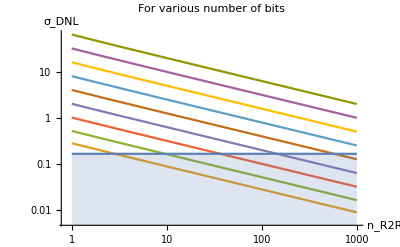

```mathematica
With[{σn=0.125, nr2r=1000},p1=ListLogLogPlot[Table[Table[{n,R2R`σDNL[i, σLogNormal[0, σn/(√n)]]},{n, 1, nr2r}],{i, 0, 9}], Joined-> True, AxesLabel-> {"n_R2R", "σ_DNL"}, PlotLabel-> "For various number of bits"];p2=LogLogPlot[0.5/3, {i, 1, nr2r}, Filling->10^-3];
Show[p1, p2]]
```

```mathematica
Module[{B=10,σn=0.125,res1, res2, res3, res4},res1=Table[Subscript[σ, l]/.(Solve[(R2R`σDNL[b, Subscript[σ, l]])^2== (0.5/3)^2&&Subscript[σ, l]>0, Subscript[σ, l], Reals][[1,1]]), {b, 1, B-1}];
res2={R2R`σDNL[#, res1[[#]]],σNormal[1, res1[[#]]],(σn/σNormal[1, res1[[#]]])^2}&/@Range[1, B-1];
res3=StandardDeviation[TransformedDistribution[R2R`DNL[#], Table[Subscript[α, i]\[Distributed]LogNormalDistribution[0, res2[[#,2]]], {i, 0, #}]]]&/@Range[1, B-1];
res4={#+1, res2[[#,3]], res2[[#,1]], res3[[#]], R2R`cost[#+1,res2[[#,3]]] }&/@Range[1,B-1];
Grid[Transpose[Join[{{"B", Subscript[n, R2R], Subscript[σDNL, lApprox], Subscript[σDNL, lExact], cost}},res4]], Dividers-> {2-> True, False}]
]
```

B | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
n_R2R | 2.82343 | 9.57766 | 36.5818 | 144.586 | 576.59 | 2304.59 | 9216.6 | 36864.6 | 147457.
σDNL_lApprox | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667
σDNL_lExact | 0.167407 | 0.166947 | 0.166757 | 0.166694 | 0.166675 | 0.166669 | 0.166667 | 0.166667 | 0.166667
cost | 16.9406 | 76.6213 | 365.818 | 1735.03 | 8072.26 | 36873.5 | 165899. | 737292. | 3.24405×10^6

### Thermometer mismatch

For thermometer code, every bit is an LSB. So the DNL is given by
(I_0(α_i+α_(i-1))-I_0 α_(i-1))/I_0-1=α_i-1

The distribution of DNL for various σ/n is plotted below.

```mathematica
errDistThermometer[σ_]:=TransformedDistribution[α-1,α\[Distributed]LogNormalDistribution[0, σ]]
```

```mathematica
plotList=Table[With[{σ=0.125/n},probValid = Probability[Abs[x]≤ 0.5, x\[Distributed]errDistThermometer[σ]];
Plot[PDF[errDistThermometer[σ], x], {x, -1, 1}, AxesLabel-> {"DNL", "PDF"}, PlotLabel-> "n^2="<>ToString[n^2]<>", P(|DNL|≤0.5)="<>ToString[probValid], PlotRange->All]], {n, 1, 2, 0.1}];
```

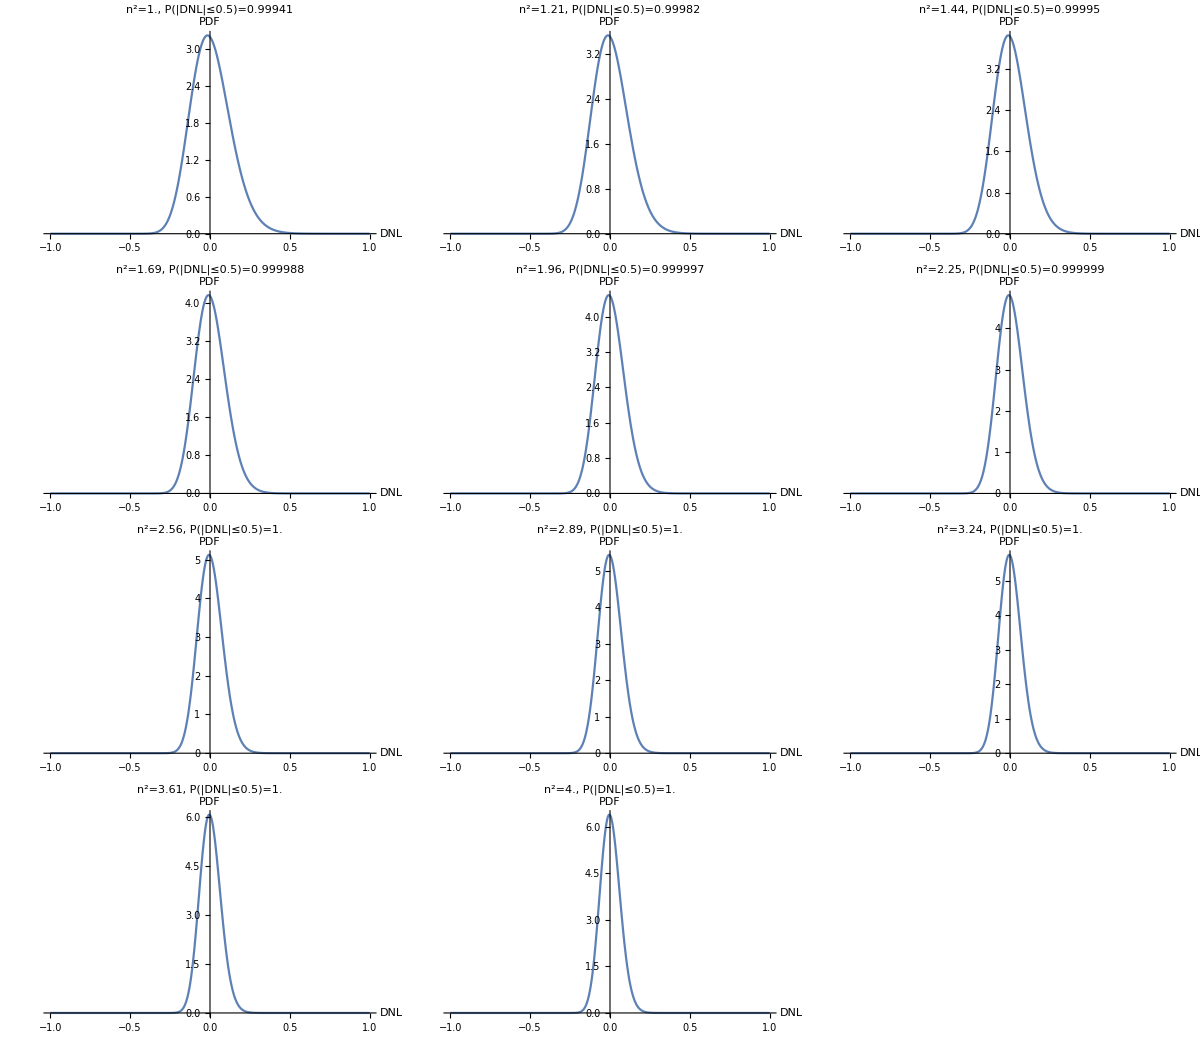

```mathematica
GraphicsGrid[ArrayReshape[plotList, {4, 3}], ImageSize->Full, Spacings-> {0, 0}]
```

So, 2048 transistors will give me better linearity than the best R-2R with way lesser number of transistors.

Note that, for a Normal random variable, 4σ has the probability

```mathematica
N[Probability[Abs[x]≤ 4 σ, x\[Distributed]NormalDistribution[0, σ]],12]
```

0.999936657516

### Segmented

The DNL is (α_M I_ref-(I_ref-α_T I_0))/I_0-1, where I_ref is the total current fed into the R-2R network.
For B bits of R-2R network, I_0 is given by I_ref/((1+α_T)(Π_(i=1))^(B-1)(1+α_i))

```mathematica
dnlSegmented[b_]:=Simplify[(Subscript[α, M] Subscript[I, ref]-(Subscript[I, ref]-Subscript[α, T] Subscript[I, 0]))/Subscript[I, 0]-1/.Subscript[I, ref]-> sumCurrent[b], Subscript[α, _]>0]
segmentedStd[b_, σnr2r_, σntherm_]:= StandardDeviation[TransformedDistribution[dnlSegmented[b]/.Subscript[α, T]-> Subscript[α, 0],Insert[Subscript[α, #]\[Distributed]LogNormalDistribution[0, σnr2r]&/@Range[0,b], Subscript[α, M]\[Distributed]LogNormalDistribution[0, σntherm], 1]]]
segmentedMean[b_, σnr2r_, σntherm_]:= Mean[TransformedDistribution[dnlSegmented[b]/.Subscript[α, T]-> Subscript[α, 0],Insert[Subscript[α, #]\[Distributed]LogNormalDistribution[0, σnr2r]&/@Range[0,b], Subscript[α, M]\[Distributed]LogNormalDistribution[0, σntherm], 1]]]
```

For 1-bit R-2R, this gives σ and μ  (for an area multiple n_R2R for R-2R and n_T for Thermometer) as

```mathematica
Subscript[σ, DNL]-> FullSimplify[segmentedStd[1, σn/(√Subscript[n, R2R]), σn/(√Subscript[n, T])],σn>0&&Subscript[n, R2R]>0&&Subscript[n, T]>0]
Subscript[μ, DNL]-> FullSimplify[segmentedMean[1, σn/(√Subscript[n, R2R]), σn/(√Subscript[n, T])],σn>0&&Subscript[n, R2R]>0&&Subscript[n, T]>0]
```

σ_DNL→√(-ⅇ^(σn^2/n_R2R)-2 ⅇ^((3 σn^2)/(2 n_R2R))+2 ⅇ^((5 σn^2)/(2 n_R2R))+ⅇ^((4 σn^2)/n_R2R)-6 ⅇ^(σn^2 (1/n_R2R+1/n_T))+2 ⅇ^(2 σn^2 (1/n_R2R+1/n_T))+2 ⅇ^(1/2 σn^2 (2/n_R2R+1/n_T))-ⅇ^(σn^2 (2/n_R2R+1/n_T))+ⅇ^(2 σn^2 (2/n_R2R+1/n_T))+6 ⅇ^(1/2 σn^2 (3/n_R2R+1/n_T))-6 ⅇ^(1/2 σn^2 (5/n_R2R+1/n_T))-2 ⅇ^(1/2 σn^2 (8/n_R2R+1/n_T))-4 ⅇ^(1/2 σn^2 (1/n_R2R+2/n_T))+4 ⅇ^(σn^2 (1/n_R2R+2/n_T))+4 ⅇ^(1/2 σn^2 (1/n_R2R+4/n_T))+4 ⅇ^(1/2 σn^2 (5/n_R2R+4/n_T))+ⅇ^((2 σn^2)/n_T)-ⅇ^(σn^2/n_T) (1+4 ⅇ^((3 σn^2)/(2 n_R2R))))

μ_DNL→-2+(1+ⅇ^(σn^2/(2 n_R2R))) (-ⅇ^(σn^2/(2 n_R2R))+ⅇ^(σn^2/(2 n_T))+ⅇ^((σn^2 (n_R2R+n_T))/(2 n_R2R n_T)))

Assuming, the mismatch is Normal (for simpler analysis and because the variance is pretty tight as it is)

```mathematica
segmentedStdNormal[b_, σlr2r_, σltherm_]:= StandardDeviation[TransformedDistribution[dnlSegmented[b]/.Subscript[α, T]-> Subscript[α, 0],Insert[Subscript[α, #]\[Distributed]NormalDistribution[1, σlr2r]&/@Range[0,b], Subscript[α, M]\[Distributed]NormalDistribution[1, σltherm], 1]]]
segmentedMeanNormal[b_, σlr2r_, σltherm_]:= Mean[TransformedDistribution[dnlSegmented[b]/.Subscript[α, T]-> Subscript[α, 0],Insert[Subscript[α, #]\[Distributed]NormalDistribution[1, σlr2r]&/@Range[0,b], Subscript[α, M]\[Distributed]NormalDistribution[1, σltherm], 1]]]
```

for 1-bit R-2R, this gives σ and μ as

```mathematica
Overscript[Subscript[σ, DNL], 2]-> FullSimplify[segmentedStdNormal[1, σLogNormal[σn/(√nR2R)], σLogNormal[σn/(√nTherm)]]^2, σn>0&&nR2R>0&&nTherm>0]
Subscript[μ, DNL]-> FullSimplify[segmentedMeanNormal[1, σLogNormal[σn/(√nR2R)], σLogNormal[σn/(√nTherm)]]]
```

σ_DNL^2→-ⅇ^(σn^2/nR2R)+ⅇ^((2 σn^2)/nR2R)-2 ⅇ^((3/nR2R+2/nTherm) σn^2)-16 ⅇ^(σn^2/nTherm)+16 ⅇ^((2 σn^2)/nTherm)+8 ⅇ^(((nR2R+nTherm) σn^2)/(nR2R nTherm))+9 ⅇ^((2 (nR2R+nTherm) σn^2)/(nR2R nTherm))-8 ⅇ^(((2 nR2R+nTherm) σn^2)/(nR2R nTherm))-9 ⅇ^(((nR2R+2 nTherm) σn^2)/(nR2R nTherm))+ⅇ^((2 (nR2R+2 nTherm) σn^2)/(nR2R nTherm))+2 ⅇ^(((nR2R+3 nTherm) σn^2)/(nR2R nTherm))-ⅇ^(((nR2R+4 nTherm) σn^2)/(nR2R nTherm))

μ_DNL→0

or in terms of the equivalent LogNormal’s standard deviation as

```mathematica
segmentedStdNormalClosed[b_, σlr2r_, σlth_]:= √(σlr2r^2+(4+σlr2r^2)^(b+1)σlth^2);
Overscript[Subscript[σ, DNL], 2]->segmentedStdNormalClosed[b,Subscript[σl, R2R], Subscript[σl, Thermo]]^2
```

σ_DNL^2→σl_R2R^2+(4+σl_R2R^2)^(1+b) σl_Thermo^2

When σl_R2R^2 is small, this is approximately

```mathematica
segmentedStdNormalApprox[b_, σlr2r_, σlth_]=segmentedStdNormalClosed[b,Subscript[σl, R2R], Subscript[σl, Thermo]]/.(4+Subscript[σl, R2R]^2)-> 4;
Overscript[Subscript[σ, DNL], 2]->segmentedStdNormalApprox[b,Subscript[σl, R2R], Subscript[σl, Thermo]]^2
```

σ_DNL^2→σl_R2R^2+4^(1+b) σl_Thermo^2

This gives the relationship between σl_R2R and σl_Thermo for 3 σ_DNL=0.5 as:

```mathematica
σlThermo[b_,σlr2r_, σtarget_]=Subscript[σl, Thermo]/.Refine[Solve[segmentedStdNormalClosed[b,σlr2r, Subscript[σl, Thermo]]^2== (σtarget)^2&&b∈Integers&&σtarget∈Reals&&σlr2r∈Reals&&Subscript[σl, Thermo]∈Reals, Subscript[σl, Thermo]],b∈Integers&&σtarget>0&&σlr2r>0&&Subscript[σl, Thermo]>0][[2,1]];
σlThermo[b,σlr2r, 0.5/3]/.σlr2r-> Subscript[σl, R2R]
```

ConditionalExpression[√(0.0277778-σl_R2R^2) (4+σl_R2R^2)^(1/2 (-1-b)),σl_R2R≤0.166667]

Then, the net cost, in terms of number of transistors is given by

```mathematica
nThermo[b_,σn_, nr2r_, σtarget_]:= (σn/σlThermo[b,σLogNormal[σn/(√nr2r)], σtarget])^2;
costR2R[b_, nr2r_]:= 2(b+2)nr2r;
costThermo[b_, nt_]:= 2^(9-b) nt;
costSegmented[b_, σn_,nr2r_, nt_]:=costR2R[b, nr2r]+costThermo[b, nt];
costSegmentedOptimized[b_, σn_,nr2r_, σtarget_]= FullSimplify[costSegmented[b, σn,nr2r, nThermo[b,σn, nr2r,σtarget]]];
costSegmentedOptimized[b, σn,nr2r, 0.5/3]
```

ConditionalExpression[2 (2+b) nr2r+(2^(9-b) (4-ⅇ^(σn^2/nr2r)+ⅇ^((2 σn^2)/nr2r))^(1+b) σn^2)/(0.0277778+ⅇ^(σn^2/nr2r)-ⅇ^((2 σn^2)/nr2r)),√(ⅇ^(σn^2/nr2r) (-1+ⅇ^(σn^2/nr2r)))≤0.166667]

which, in the limit  σn^2≪n_R2R  is:

```mathematica
costSegmentedBestEstimate[b_, σn_,nr2r_,σtarget_]=Refine[FullSimplify[costSegmentedOptimized[b, σn,nr2r,σtarget]/.ⅇ^(σn^2/nr2r)-> 1/.ⅇ^((2 σn^2)/nr2r)-> 1], σtarget>0]
```

(2+b) nr2r+(2^(11+b) σn^2)/σtarget^2

The tradeoff is plotted below for 2, 3 and 4 R-2R bits for σ_DNL≤0.5/3

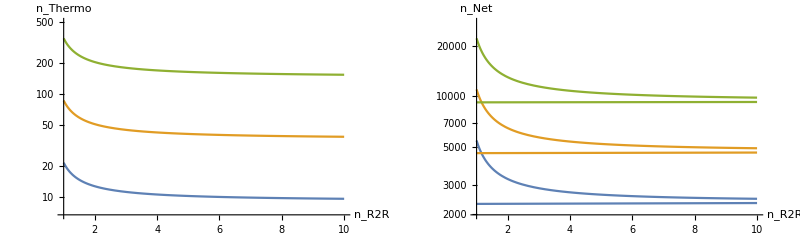

```mathematica
GraphicsRow[With[{σn=0.125},{LogPlot[Evaluate[Assuming[√(ⅇ^(σn^2/nr2r) (-1+ⅇ^(σn^2/nr2r)))≤0.5/3,Simplify[nThermo[b, σn,nr2r,0.5/3]/.b-> Range[3]]]], {nr2r,1,10}, PlotRange-> All, AxesLabel-> {"n_R2R", "n_Thermo"}],pa=LogPlot[Evaluate[Assuming[√(ⅇ^(σn^2/nr2r) (-1+ⅇ^(σn^2/nr2r)))≤0.5/3,Simplify[costSegmentedOptimized[b, σn,nr2r,0.5/3]/.b-> Range[3]]]], {nr2r,1,10}, PlotRange-> All, AxesLabel-> {"n_R2R", "n_Net"}];pb=LogPlot[Evaluate[Assuming[√(ⅇ^(σn^2/nr2r) (-1+ⅇ^(σn^2/nr2r)))≤0.5/3,Simplify[costSegmentedBestEstimate[b, σn,nr2r,0.5/3]/.b-> Range[3]]]], {nr2r,1,10}, PlotRange-> All, AxesLabel-> {"n_R2R", "n_Net"}];Show[pa, pb]}], ImageSize->Full]
```

Calculated total costs (for σ_DNL≤0.5) are given below:

```mathematica
costTable=With[{σn=0.125}, Table[{b+1, nr2r, nThermo[b, σn,nr2r,0.5/3], costSegmentedOptimized[b, σn,nr2r,0.5/3]},{nr2r,1, 10},{b, 1, 9}]];
Table[costTable[[nr2r,br2r,4]],{nr2r, 1, Length[costTable]},{br2r, 1, Length[costTable[[1]]]}];
Join[{#+1&/@Range[Length[costTable[[1]]]]}, %];
Join[{ #&/@Join[{Subscript[n, R2R]/Subscript[B, R2R]},Range[Length[costTable]]]}, Transpose[%]];
Grid[%]
```

n_R2R/B_R2R | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
2 | 5478.51 | 3239.16 | 2857.3 | 2700.87 | 2616.68 | 2564.7 | 2529.86 | 2505.23 | 2487.17 | 2473.58
3 | 10998.8 | 6487.11 | 5716.07 | 5399.03 | 5227.45 | 5120.73 | 5048.53 | 4996.89 | 4958.48 | 4929.07
4 | 22082.6 | 12993.8 | 11438.1 | 10796.6 | 10448.1 | 10230.1 | 10081.7 | 9974.65 | 9894.23 | 9831.97
5 | 44337.7 | 26031. | 22894.2 | 21598.4 | 20892.5 | 20449.6 | 20146.6 | 19927. | 19761. | 19631.6
6 | 89024.9 | 52154.7 | 45833.4 | 43219.3 | 41792.8 | 40895.8 | 40280.8 | 39833.5 | 39494.2 | 39228.5
7 | 178756. | 104504. | 91769.1 | 86499.4 | 83621.1 | 81809.1 | 80564.6 | 79658. | 78968.8 | 78427.7
8 | 358934. | 209406. | 183758. | 173141. | 167338. | 163683. | 161170. | 159338. | 157943. | 156847.
9 | 720731. | 419624. | 367974. | 346589. | 334899. | 327532. | 322465. | 318768. | 315952. | 313736.
10 | 1.44722×10^6 | 840888. | 736887. | 693824. | 670280. | 655438. | 645228. | 637776. | 632098. | 627628.

The contour plots of |σ_DNL-0.5| for 2, 3, and 4 bit R-2R (using Gaussian approximation) are given below:

```mathematica
plotSegmentedσ=With[{σn=0.125},ContourPlot[Abs[3segmentedStdNormalClosed[#1, σn/(√Subscript[n, R2R]),σn/(√Subscript[n, T])]- 0.5],{Subscript[n, R2R], #2[[1]], #2[[2]]}, {Subscript[n, T], #3[[1]], #3[[2]]}, FrameLabel->Automatic, PlotLabel-> "B = "<>ToString[#1+1], ColorFunctionScaling->False]]&;
```

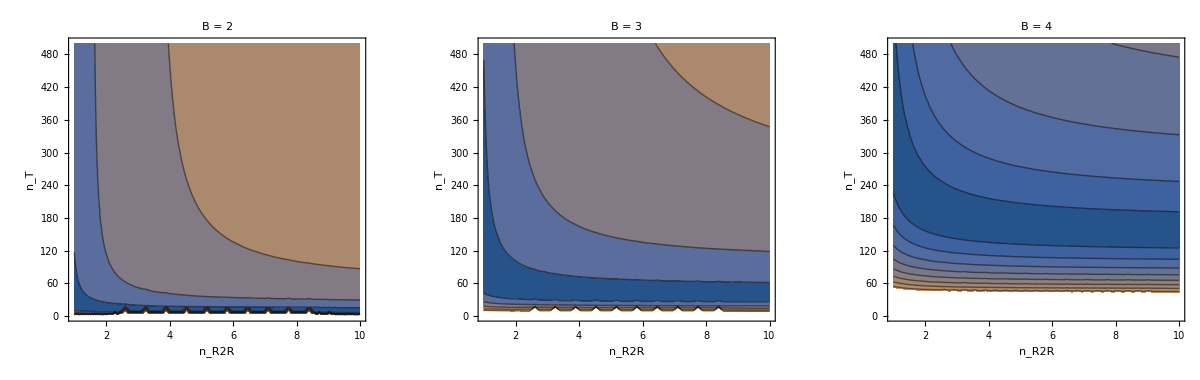

```mathematica
GraphicsRow[plotSegmentedσ[#, {1, 10},{1, 500}]&/@{1, 2, 3}, ImageSize->Full]
```

The cost contour as  a function of number of R-2R bits and cost of R-2R is given below

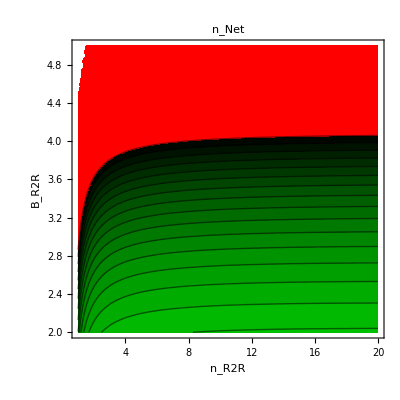

```mathematica
With[{σn=0.125},ContourPlot[costSegmentedOptimized[b-1, σn,Subscript[n, R2R],#1],{Subscript[n, R2R], #2[[1]], #2[[2]]}, {b, #3[[1]], #3[[2]]}, FrameLabel->{"n_R2R","B_R2R"}, PlotLabel-> "n_Net", Contours-> Range[1000, 10000, 500],ColorFunction-> (If[#<10000, Hue[1/3, 1, 1-#/10000], Hue[1]]&),ColorFunctionScaling->False]]&[0.5/3, {1, 20}, {2, 5}]
```

### Thermometer INL

The output current for DAC value of n is

```mathematica
outNth[n_]:=Subscript[I, 0] Sum[Subscript[α, j] , {j, 0, n}];
outNth[n]
```

I_0 ∑_(j=0)^n α_j

Then, the linear approximation of the input-output is given by
I_n=m I_0 + c, where

```mathematica
ThermoLinearFit[n_]:={Simplify[(outNth[n]-Subscript[α, 0] Subscript[I, 0])/(n Subscript[I, 0])], Simplify[Subscript[α, 0] Subscript[I, 0]+(-outNth[n]+Subscript[I, 0] Subscript[α, 0])/n]}/;n> 0 || ¬NumberQ[n]
Grid[{#[[2]]-> #[[1]]}&/@Transpose[{ThermoLinearFit[n], {m, c}}], Alignment->Left]
```

m→(-α_0+∑_(j=0)^n α_j)/n
c→(I_0 ((1+n) α_0-∑_(j=0)^n α_j))/n

Then, the INL (as a fraction of LSB) is given by (I_out[n]-I_fit[n])/I_0

```mathematica
INLThermometer[i_, {x_, y_}]:=Simplify[outNth[i]-{x, y} .{(i+1)Subscript[I, 0], 1}]/Subscript[I, 0];
INLThermometer[i, ThermoLinearFit[n]]
```

((i-n) α_0+n ∑_(j=0)^i α_j-i ∑_(j=0)^n α_j)/n

This is equivalent to

```mathematica
Sum[Subscript[α, j], {j, 1, i}]-i/n Sum[Subscript[α, j], {j, 1, n}]
(1-i/n)Sum[Subscript[α, j],{j, 1, i}]-i/n Sum[Subscript[α, j], {j, i+1, n}]
```

∑_(j=1)^i α_j-(i ∑_(j=1)^n α_j)/n

(1-i/n) ∑_(j=1)^i α_j-(i ∑_(j=1+i)^n α_j)/n

Since α_j are i.i.d, the standard deviation of the INL as a function of i and n is then approximately given by

```mathematica
STDINLThermometer[i_, n_, σl_]:= √((1-i/n)^2 i +(i/n)^2(n-i))σl;
Subscript[σ, INL]-> STDINLThermometer[i, n, Subscript[σ, l]]
```

σ_INL→√(i (1-i/n)^2+(i^2 (-i+n))/n^2) σ_l

The maximum error occurs for i→n/2and is:

```mathematica
STDINLThermometer[n/2, n, σn]
```

(√n σn)/2

σ_INL as a function of i for n→1023 is plotted below

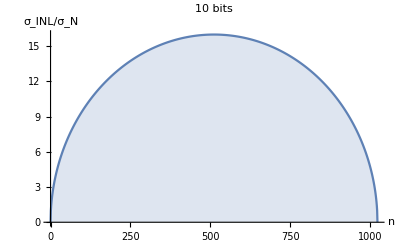

```mathematica
DiscretePlot[STDINLThermometer[i, 1023,1], {i, 0, 1023}, AxesLabel->{"n", "σ_INL/σ_N"}, PlotLabel-> "10 bits"]
```

#### Example:

For n→1023 and σ_n→0.0625

```mathematica
With[{σn=0.125/2},alphaList = Insert[(Subscript[α, #]-> RandomVariate[LogNormalDistribution[0, σn]]&/@Range[1, 1023]), Subscript[α, 0]-> 1, 1];
ys=(outNth[#]&/@Range[0, 1023])/.alphaList;
fits = {(ys[[-1]]/Subscript[I, 0]-1)/1023, Subscript[I, 0]+(-ys[[-1]]+Subscript[I, 0])/1023}.{Subscript[I, 0] Range[1, 1024],1&/@Range[0, 1023]};]
```

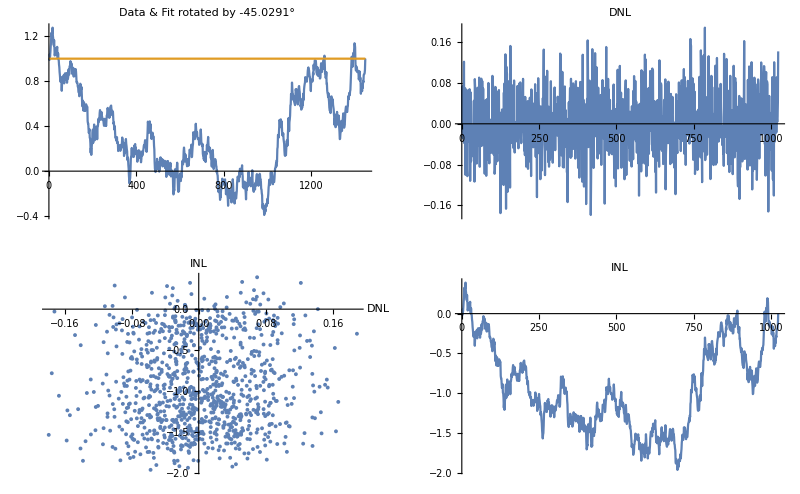

```mathematica
Module[{dnl = Differences[ys/Subscript[I, 0]]-1, inl=(ys-fits)/Subscript[I, 0], dataRotated = RotationTransform[-ArcTan[(ys[[-1]]/Subscript[I, 0]-1)/1023],{1, 1}][Transpose[{Range[1024],ys/Subscript[I, 0]}]], fitRotated= RotationTransform[-ArcTan[(ys[[-1]]/Subscript[I, 0]-1)/1023],{1, 1}][Transpose[{Range[1024],fits/Subscript[I, 0]}]]},
GraphicsGrid[{{ListLinePlot[{dataRotated, fitRotated}, PlotMarkers->{Automatic, 0.1} ,PlotLabel-> "Data & Fit rotated by "<> ToString[-ArcTan[(ys[[-1]]/Subscript[I, 0]-1)/1023]/Degree]<>"°"],
ListLinePlot[dnl, PlotLabel-> "DNL"]},
{ListPlot[Transpose[{dnl,inl [[2;;]]}], AxesLabel-> {DNL, INL}],ListLinePlot[inl, PlotLabel-> "INL"]}}, ImageSize-> Full]]
```

### Scratchpad

σ of effective number of bits:

TransformedDistribution[Log[x]/Log[2],x\[Distributed]NormalDistribution[1+n,√n σn]]

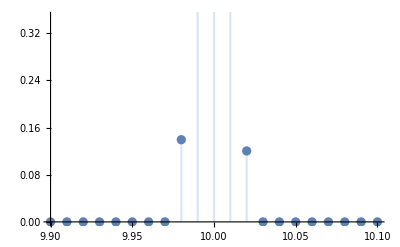

$Aborted

```mathematica
TransformedDistribution[Log2[rv], rv\[Distributed]NormalDistribution[n+1, √n σn]]
DiscretePlot[PDF[%/.{n-> 1023, σn-> 0.125}, x], {x, 9.9, 10.1, 0.01}]
```

The variance of R-2R for 1 to 5 bits:

```mathematica
Grid[Table[{b->FullSimplify[R2RStd[b, σn], σn>0]}, {b, 0, 4}]]
```

0→√(ⅇ^(σn^2) (-1+ⅇ^(σn^2)))
1→√(ⅇ^(σn^2) (-1+4 ⅇ^(σn^2/2)-3 ⅇ^(σn^2)-4 ⅇ^((3 σn^2)/2)+4 ⅇ^(3 σn^2)))
2→√(ⅇ^(σn^2) (-1+ⅇ^(σn^2) (5+4 ⅇ^(σn^2) (-4+2 ⅇ^(σn^2)+ⅇ^(3 σn^2)))))
3→√(ⅇ^(σn^2) (-1-4 ⅇ^(σn^2/2)+ⅇ^(σn^2)+16 ⅇ^((3 σn^2)/2)-8 ⅇ^(2 σn^2)-36 ⅇ^((5 σn^2)/2)+8 ⅇ^(3 σn^2)+16 ⅇ^((7 σn^2)/2)-16 ⅇ^(4 σn^2)+12 ⅇ^(5 σn^2)+8 ⅇ^((11 σn^2)/2)+4 ⅇ^(7 σn^2)))
4→√(ⅇ^(σn^2) (-1-8 ⅇ^(σn^2/2)-15 ⅇ^(σn^2)+16 ⅇ^((3 σn^2)/2)+36 ⅇ^(2 σn^2)-40 ⅇ^((5 σn^2)/2)-60 ⅇ^(3 σn^2)+32 ⅇ^((7 σn^2)/2)-4 ⅇ^(4 σn^2)-64 ⅇ^((9 σn^2)/2)+24 ⅇ^(5 σn^2)+48 ⅇ^((11 σn^2)/2)+16 ⅇ^(7 σn^2)+16 ⅇ^((15 σn^2)/2)+4 ⅇ^(9 σn^2)))

```mathematica
Mean[TransformedDistribution[(rv1-ⅇ^(σn^2/2))(rv1 rv2-ⅇ^(1+σn^2)),  {rv1\[Distributed]LogNormalDistribution[1, σn], rv2\[Distributed]LogNormalDistribution[0, σn]}]]
```

ⅇ^(2+(3 σn^2)/2) (-1+ⅇ^(σn^2))

```mathematica
deltaBit[1]
Ex[#]&/@Expand[%^2]-Expand[(Ex[#]&/@Expand[%])^2]
%/.Ex[n_]:> n/;NumberQ[n]
```

-2+α_1 (1+α_T)

-Ex[-2]^2+Ex[4]+Ex[-4 α_1]-2 Ex[-2] Ex[α_1]-Ex[α_1]^2+Ex[α_1^2]+Ex[-4 α_1 α_T]-2 Ex[-2] Ex[α_1 α_T]-2 Ex[α_1] Ex[α_1 α_T]-Ex[α_1 α_T]^2+Ex[2 α_1^2 α_T]+Ex[α_1^2 α_T^2]

Ex[-4 α_1]+4 Ex[α_1]-Ex[α_1]^2+Ex[α_1^2]+Ex[-4 α_1 α_T]+4 Ex[α_1 α_T]-2 Ex[α_1] Ex[α_1 α_T]-Ex[α_1 α_T]^2+Ex[2 α_1^2 α_T]+Ex[α_1^2 α_T^2]

```mathematica
Grid[{branchCurrent[#]}&/@{0, 1, 2, 3}]
```

I_0
I_0 α_1 (1+α_T)
I_0 (1+α_1) α_2 (1+α_T)
I_0 (1+α_1) (1+α_2) α_3 (1+α_T)

```mathematica
Grid[{Simplify[ExpandAll[deltaBit[#]]]}&/@{0,1, 2, 4}]
```

0
-2+α_1 (1+α_T)
-2+α_1 (-1+α_2) (1+α_T)+α_2 (1+α_T)
-2-α_3+α_4+α_3 α_4-α_3 α_T+α_4 α_T+α_3 α_4 α_T+α_2 (1+α_3) (-1+α_4) (1+α_T)+α_1 (1+α_2) (1+α_3) (-1+α_4) (1+α_T)

```mathematica
Grid[{Simplify[Expand[dBit[#]]]}&/@{1, 2, 4}]
```

-2+α_1 (1+α_T)
-2+α_1 (-1+α_2) (1+α_T)+α_2 (1+α_T)
-2-α_3+α_4+α_3 α_4-α_3 α_T+α_4 α_T+α_3 α_4 α_T+α_2 (1+α_3) (-1+α_4) (1+α_T)+α_1 (1+α_2) (1+α_3) (-1+α_4) (1+α_T)

```mathematica
ExpandAll[10(Log10[12]+ 2 n Log10[2])]//N
```

10.7918+6.0206 n